```mathematica
Quit[]
```

```mathematica
ρinteg[x_,T_]=(x^(1/2)(x+2/T)^(1/2)(x+1/T)^2)/(Exp[x+1/T]+1);
pinteg[x_,T_]=(x^(3/2)(x+2/T)^(3/2))/(Exp[x+1/T]+1);
```

```mathematica
AbsoluteTiming[ρList=Table[{10^lnT,NIntegrate[ρinteg[x,10^lnT],{x,0,1000},WorkingPrecision->30]},{lnT,-2,5,10^-2}];
pList=Table[{10^lnT,NIntegrate[pinteg[x,10^lnT],{x,0,1000},WorkingPrecision->30]},{lnT,-2,5,10^-2}];]
```

{14.3252,Null}

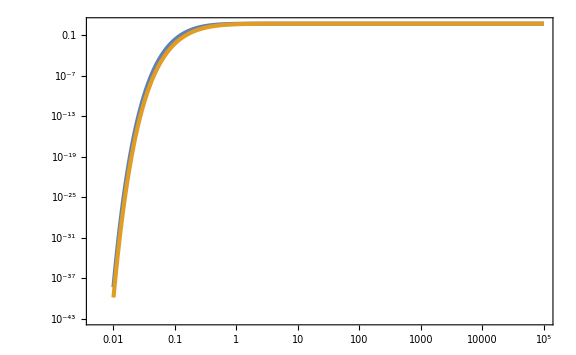

```mathematica
ListLogLogPlot[{ρList,pList}]
```

```mathematica
ρintegint[T_]=Interpolation[ρList][T];
pintegint[T_]=Interpolation[pList][T];
```

### Fiducial

```mathematica
gSM=10675/100;
gDM=2 2 10;
```

```mathematica
ρ[T_]:=π^2/30 gSM T^4+T^4/(2 π^2)ρintegint[T]gDM/;T>=10^-2
ρ[T_]:=π^2/30 gSM T^4/;T<10^-2
ρp[T_]:=π^2/30 gSM 4 T^3+ 4 T^3/(2 π^2)ρintegint[T]gDM+T^4/(2 π^2)ρintegint'[T]gDM/;T>=10^-2
ρp[T_]:=π^2/30 gSM 4 T^3/;T<10^-2
p[T_]:=1/3 π^2/30 gSM T^4+T^4/(6 π^2)pintegint[T]gDM/;T>=10^-2
p[T_]:=1/3 π^2/30 gSM T^4/;T<10^-2
pp[T_]:=1/3 π^2/30 gSM 4 T^3+4 T^3/(6 π^2)pintegint[T]gDM+T^4/(6 π^2)pintegint'[T]gDM/;T>=10^-2
pp[T_]:=1/3 π^2/30 gSM 4 T^3/;T<10^-2
s[T_]:=(ρ[T]+p[T])/T
w[T_]:=p[T]/ρ[T]
cs2[T_]:=pp[T]/ρp[T]
gr[T_]:=ρ[T]/(π^2/30 T^4)
gs[T_]:=s[T]/((2 π^2)/45 T^3)
```

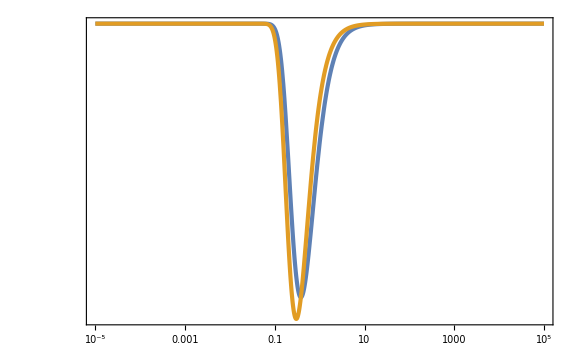

```mathematica
LogLogPlot[{w[T],cs2[T]},{T,10^-5,10^5},PlotRange->Full]
```

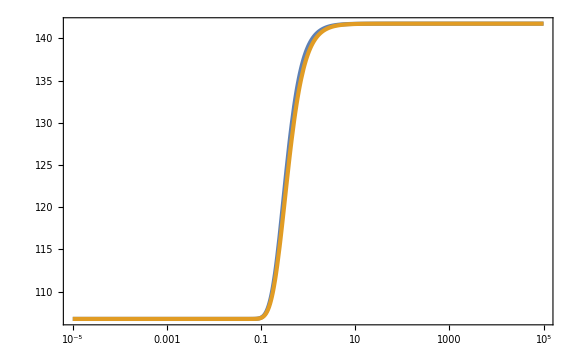

```mathematica
LogLinearPlot[{gr[T],gs[T]},{T,10^-5,10^5}]
```

```mathematica
Tin=10^5;
Tout=10^-5;
ain=1;
sin=s[Tin]
a[T_]:=ain sin^(1/3)/s[T]^(1/3)
```

6.21785077266962926319918931474×10^16

```mathematica
AbsoluteTiming[NρList=Table[{Log[a[10^lnT]],ρ[10^lnT]},{lnT,Log[Tout],Log[Tin],10^-2}]//Quiet;
NwList=Table[{Log[a[10^lnT]],w[10^lnT]},{lnT,Log[Tout],Log[Tin],10^-2}]//Quiet;
NgrList=Table[{Log[a[10^lnT]],gr[10^lnT]},{lnT,Log[Tout],Log[Tin],10^-2}]//Quiet;
NgsList=Table[{Log[a[10^lnT]],gs[10^lnT]},{lnT,Log[Tout],Log[Tin],10^-2}]//Quiet;]
```

{8.55687,Null}

```mathematica
ρint[NN_]=Interpolation[NρList][NN];
wint[NN_]=Interpolation[NwList][NN];
grint[NN_]=Interpolation[NgrList][NN];
gsint[NN_]=Interpolation[NgsList][NN];
```

```mathematica
Nout=Log[a[Tout]]//Quiet
```

23.120376026772605860925213207311

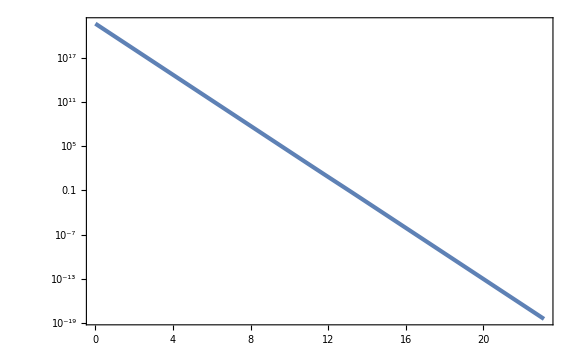

```mathematica
LogPlot[ρint[NN],{NN,0,Nout}]
```

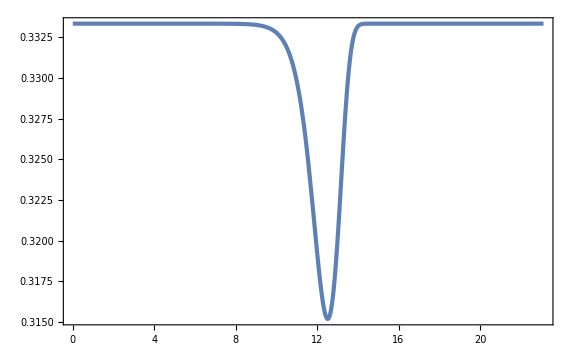

```mathematica
Plot[wint[NN],{NN,0,Nout},PlotRange->Full]
```

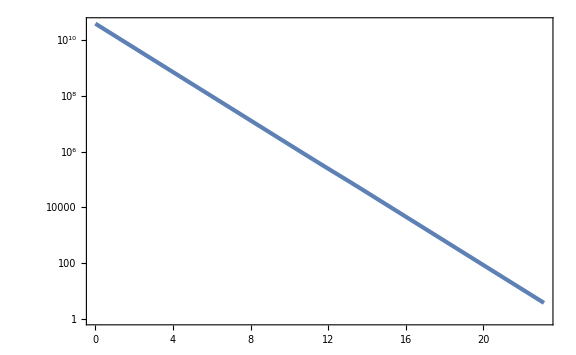

```mathematica
LogPlot[Exp[NN]Sqrt[ρint[NN]/3],{NN,0,Nout}]
```

```mathematica
TkList=ParallelTable[Tp0=0;
ks=Exp[Nk]Sqrt[ρint[Nk]/3];
Ni=Nk-5;(*Nf=Nk+5;*)
sol=NDSolve[{T''[NN]+3/2(1-wint[NN])T'[NN]+k^2/(Exp[2NN]ρint[NN]/3)T[NN]==0/.{k->ks},T[0]==1,T'[0]==0,WhenEvent[T''[NN]==0,Tp0++;If[Tp0>=10,Nfs=NN;"StopIntegration"]]},T'[NN],{NN,0,Nout},WorkingPrecision->30,MaxSteps->100000][[1]]//Quiet;
Tpsol[NN_]=T'[NN]/.sol;
{ks/(a[1]Sqrt[ρ[1]/3]),Tpsol[Nfs]^2(grint[Nfs] gsint[Nfs]^(-4/3))/106.75^(-1/3)}
,{Nk,7,18,10^-1}];//AbsoluteTiming
```

{23.3213,Null}

```mathematica
OGWg=Table[{(Exp[Nk]Sqrt[ρint[Nk]/3])/(a[1]Sqrt[ρ[1]/3]),(grint[Nk] gsint[Nk]^(-4/3))/106.75^(-1/3)},{Nk,7,18,0.01}];
```

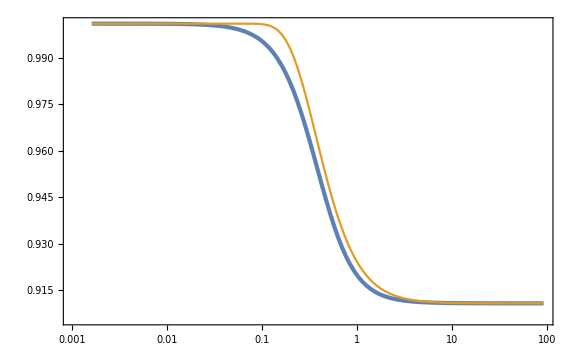

```mathematica
Show[ListLogLinearPlot[TkList],ListLogLinearPlot[OGWg.{{1,0},{0,Last[TkList][[2]]}},PlotStyle->Color[2]]]
```